## Gaussian moving potential

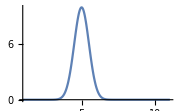

```mathematica
Gaus[a_, b_, c_, x_, midx_, ω_, t_]:= N[Chop[a*Exp[Chop[(-(x-midx- b*Sin[ω*t])^2)/(2*c^2)]]]];
Plot[{Gaus[10, 3, 0.5,  5,x, 1, 0]}, {x, 1, 11}, PlotRange->Full, ImageSize-> Small]
```

```mathematica
Ht[Nl_,a_, b_, c_,  ω_, t_]:=Table[If[i==j, Gaus[a, b, c, Ceiling[Nl/2], i, ω, t],If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Ht[7,1, 1, 0.5, 1, 0]//MatrixForm
```

(1.523×10^-8 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0.000335463 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0.135335 | -1 | 0 | 0 | 0
0 | 0 | -1 | 1. | -1 | 0 | 0
0 | 0 | 0 | -1 | 0.135335 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0.000335463 | -1
0 | 0 | 0 | 0 | 0 | -1 | 1.523×10^-8)

```mathematica
ClearAll@ψ;
tf = 30;
Nl = 61;
midx = Ceiling[Nl/2];
a = 100;
b = 3;
c = 3;
ω = 12;
ψ0 = Table[If[i==midx,1,0],{i,1,Nl}];
s=NDSolve[{I D[ψ[t], t]== Ht[Nl,a, b, c, ω, t].ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s];
```

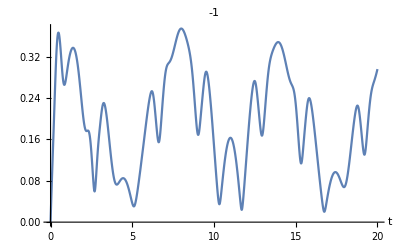
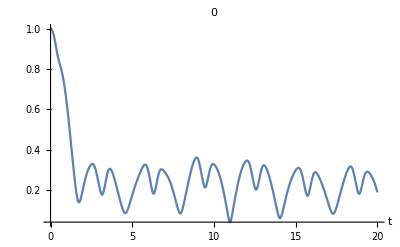
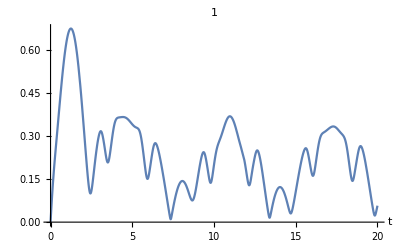

```mathematica
Table[Plot[Norm[ ψ[t][[1, i]]], {t, 0, tf},PlotRange ->Full, PlotLabel -> i - midx, AxesLabel->{"t", ""}], {i, midx - 1, midx+1}]
```

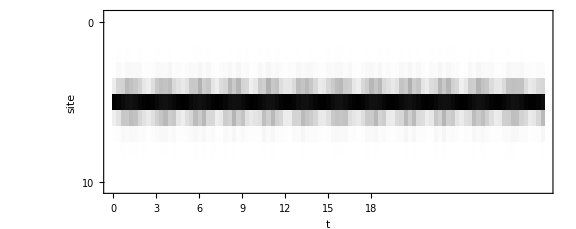

Period: 0.523599

```mathematica
siteside = Floor[Nl/2];
siteside = 5;
tmax = 30;
xrow=Table[If[Divisible[i, 10]==True,i/10,""],{i,0,tf*10}];
ycolumn=Table[ If[Divisible[i, 10]==True,i,""],{i,0,siteside*2}];
xticks=MapIndexed[{#2[[1]],#}&,xrow];
yticks=MapIndexed[{#2[[1]],#}&,ycolumn];
MatrixPlot[Table[Norm[ψ[t][[1, i]]], {i, midx-siteside, midx+siteside}, {t, 0, tmax, 0.1}], FrameLabel->{"site","t"}, FrameTicks->{{yticks,yticks},{xticks,xticks}}, ImageSize-> Large, ColorFunctionScaling->False]
Print["Period: ", N[2*Pi/ω]]
```